```mathematica
(* Ищем u по f *)
```

```mathematica
k[x_]:=If[x<=1/2,1,3/2];
f[x_]:=Sin[x];
```

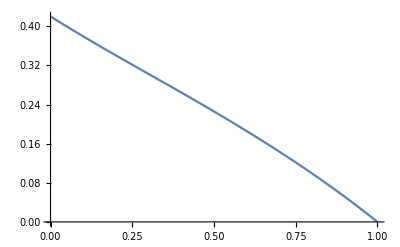

```mathematica
sol1[y_]:=(u[x]/.(DSolve[-D[3/2*D[u[x],x],x]+u[x]==f[x]&&u[0]+u'[0]==0,u,{x,0,1/2}]))[[1]]/.{x->y,C[1]->a};
sol2[y_]:=(u[x]/.(DSolve[-D[2*D[u[x],x],x]+u[x]==f[x]&&u[1]==0,u,{x,1/2,1}]))[[1]]/.{x->y,C[1]->b};
{aa,bb}={a,b}/.Solve[sol1[1/2]==sol2[1/2]&&sol1'[1/2]==sol2'[1/2]][[1]];
ssol1[y_]:=sol1[x]/.{x->y,a->aa,b->bb};
ssol2[y_]:=sol2[x]/.{x->y,a->aa,b->bb};
sol[x_]:=If[x<=1/2,ssol1[x],ssol2[x]];
Plot[sol[z],{z,0,1}]
```

-1/2 Sin[2 π x]^2 (-1+Cos[4 π x]+8 π (4 π (1+2 Cos[4 π x]) If[2 x≤1,1,3/2]+If[2 x≤1,0,0] Sin[4 π x]))

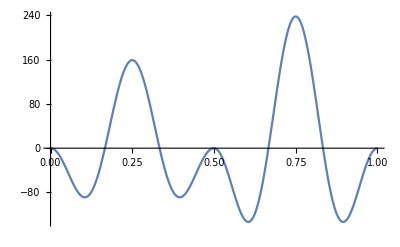

```mathematica
(* Ищем f по u *)

g[x_]:=Sin[2*Pi*x]^4;
h[x_]:=-D[k[y]*g'[y],y]+g[y]/.{y->x} 
FullSimplify[h[x]]
Plot[h[x],{x,0,1}]
```